# CEE 506 - Assignments #1

## Peter Mackenzie-Helnwein

## Problem 1-1

I placed the origin of my coordinate system underneath the sliding (right) support at the height of the lower (left) support.  x points to the right, y points up.  u is positive if the right support moves down.  P is positive pointing downward.

```mathematica
SetDirectory[$UserDocumentsDirectory];
SetDirectory["./Classes/CESG 506/Assignments/Assignment #1"];
Import["Problem1-1.png"]
```

-Graphics-

### Kinematics

#### Length, axial vectors

```mathematica
XI={-5.5, 0};
XJ={0,0.5};
ui={0,0};
uj={0,-u};
```

XI = {-4.0, 0};

```mathematica
Lvec=XJ-XI;
```

```mathematica
xi=XI+ui;
xj=XJ+uj;
```

```mathematica
lvec=xj-xi
```

{5.5,0.5-u}

```mathematica
Len2=Lvec.Lvec
```

30.5

```mathematica
L=Sqrt[Len2]
```

5.52268

```mathematica
len2=lvec.lvec
```

30.25+(0.5-u)^2

```mathematica
len=Sqrt[len2]
```

√(30.25+(0.5-u)^2)

```mathematica
Nvec=Lvec/L
```

{0.995893,0.0905357}

```mathematica
nvec=lvec/len
```

{5.5/(√(30.25+(0.5-u)^2)),(0.5-u)/(√(30.25+(0.5-u)^2))}

#### Strain

Stretch

```mathematica
λ=len/L
```

0.181071 √(30.25+(0.5-u)^2)

Traditional definition (similar to linear theory, but nonlinear)

```mathematica
ϵ1=(len-L)/L
```

0.181071 (-5.52268+√(30.25+(0.5-u)^2))

Green-Lagrange strain

```mathematica
ϵ2=1/2(len2-Len2)/Len2
```

0.0163934 (-0.25+(0.5-u)^2)

Almansi strain

```mathematica
ϵ3=1/2(len2-Len2)/len2
```

(-0.25+(0.5-u)^2)/(2 (30.25+(0.5-u)^2))

Henkey or Natural strain

```mathematica
ϵ4=1/2 Ln[len2/Len2]
```

1/2 Ln[0.0327869 (30.25+(0.5-u)^2)]

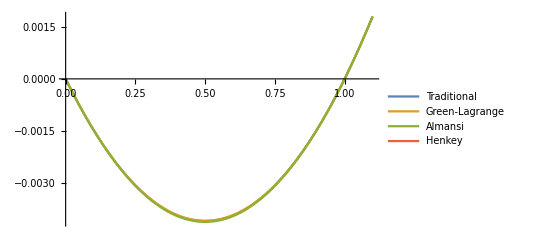

```mathematica
Plot[{ϵ1,ϵ2,ϵ3,ϵ4},{u,0,1.1},PlotRange->All,PlotLegends->{"Traditional","Green-Lagrange","Almansi","Henkey"}]
```

Reality check: the horizontal configuration should have a strain in the range of

```mathematica
(5.5-L)/L
```

-0.00410679

This comparison shows that for small strains, all options are viable and yield nearly identical results (GREAT!)

### Constitutive

We assume that the cross section area does not change with deformation.  This is not always a good assumption but it is viable with our very small strains.

```mathematica
EA=2100;
```

```mathematica
f1=EA ϵ1;
```

```mathematica
f2=EA ϵ2;
```

```mathematica
f3=EA ϵ3;
```

```mathematica
f4=EA ϵ4;
```

### Equilibrium

#### On the undeformed system

```mathematica
α0=ArcTan[Lvec⟦2⟧/Lvec⟦1⟧];
```

```mathematica
P0=-F Sin[α0]
```

-0.0905357 F

#### On the deformed system

```mathematica
Pn=-F Sin[ArcTan[lvec⟦2⟧/lvec⟦1⟧]]
```

-(0.181818 F (0.5-u))/(√(1+0.0330579 (0.5-u)^2))

### Results

#### Plots using equilibrium on the undeformed system

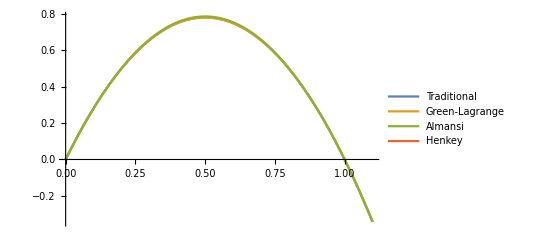

```mathematica
Plot[Evaluate[P0/.F->{f1,f2,f3,f4}],{u,0,1.1},PlotLegends->{"Traditional","Green-Lagrange","Almansi","Henkey"}]
```

Note how all options predict zero force at u=2H, which completely relaxes the bar.  However, there shouldn’t be a vertical force as u=H levels the bar.

#### Plots using equilibrium on the deformed system

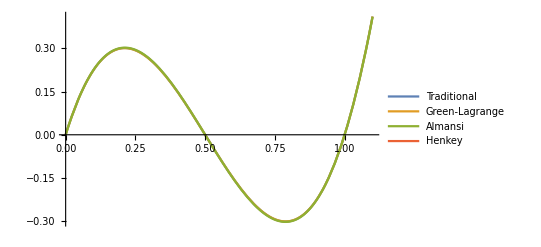

```mathematica
Plot[Evaluate[Pn/.F->{f1,f2,f3,f4}],{u,0,1.1},PlotLegends->{"Traditional","Green-Lagrange","Almansi","Henkey"}]
```

Note how all options predict zero force at u=H and at u=2H.

This problem is one where displacements are very large but the associated strain remains quite small.  As a consequence, all of the discusses strain measures yield suitable and extremely similar results.  The confidence level in the solution to this problem is thus quite high.

### Cleanup

```mathematica
Xi=.
Xj=.
ui=.
uj=.
len2=.
len=.
Len2=.
L=.
Nvec=.
nvec=.
ϵ1=.
ϵ2=.
ϵ3=.
ϵ4=.
f1=.
f2=.
f3=.
f4=.
P0=.
Pn=.
EA=.
```

## Problem 1-2

```mathematica
SetDirectory[$UserDocumentsDirectory];
SetDirectory["./Classes/CESG 506/Assignments/Assignment #1"];
Import["Problem1-2.png"]
```

-Graphics-

I approach this problem a bit more general than necessary by developing a general truss element first, then assemble the simple system, and eventually developing the solution algorithm.

### Kinematics

#### Length, axial vectors

I define everything as functions, so no values here.

```mathematica
x[X_,u_]:=X+u
```

```mathematica
LenVec[XI_,XJ_]:=XJ-XI
```

```mathematica
VecLength2[v_]:=v.v
```

```mathematica
VecLength[v_]:=Sqrt[v.v]
```

```mathematica
UnitVec[v_]:=v/VecLength[v]
```

```mathematica
Nvec[XI_,XJ_]:=UnitVec[LenVec[XI,XJ]]
```

```mathematica
nvec[XI_,XJ_,ui_,uj_]:=UnitVec[LenVec[x[XI,ui],x[XJ,uj]]]
```

```mathematica
λ2[XI_,XJ_,ui_,uj_]:=VecLength2[LenVec[x[XI,ui],x[XJ,uj]]]/VecLength2[LenVec[XI,XJ]]
```

#### Strain

Traditional definition (similar to linear theory, but nonlinear)

```mathematica
ϵ1[λ2_]:=Sqrt[λ2]-1
```

Green-Lagrange strain

```mathematica
ϵ2[λ2_]:=1/2(λ2-1)
```

Almansi strain

```mathematica
ϵ3[λ2_]:=1/2(1-1/λ2)
```

Henkey or Natural strain

```mathematica
ϵ4[λ2_]:=1/2 Log[λ2]
```

### Constitutive

This is the internal force, i.e., a scalar

```mathematica
F[EA_,ϵ_]:=EA ϵ
```

### Equilibrium

Now we need the nodal forces, i.e., the force vector.  I represent them as list of nodal vectors

```mathematica
Felem[F_, lvec_]:=Block[{nvec},
nvec=UnitVec[lvec];
{-F nvec, F nvec}
]
```

### Tangent Stiffness Matrix

The derivation is on paper

```mathematica
Kelem[lvec_,EA_,F_ ]:=Block[
{ll,nvec,ke,ntensorn},
ll=VecLength[lvec];
nvec=lvec/ll;
ntensorn=Transpose[{nvec}].{nvec};
ke=EA/ll ntensorn+F/ll(IdentityMatrix[Length[lvec]]-ntensorn);
{{ke,-ke},{-ke,ke}}
]
```

### Now to the actual problem

#### Setup

```mathematica
x1={-5.5,0.0};
x2={0.0, 0.5};
x3={4.0,0.0};
```

Debug override : make it a symmetric system

```mathematica
(*x3={5.5,0.0};*)
```

```mathematica
u1={0.0,0.0};
u2={u,v};
u3={0.0,0.0};
```

```mathematica
EA=2100;
```

Now select Henkey strain for our model:
I simply define a generic strain function that switches to Henkey strain.  Changing this function will change the choice easily.

```mathematica
ϵ[λ2_]:=ϵ4[λ2]
```

#### Elements

The left element ...

... internal force

```mathematica
F1=F[EA, ϵ[λ2[x1,x2,u1,u2]]]
```

1050 Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)]

... nodal force vector

```mathematica
Fe1=Felem[F1,LenVec[x[x1,u1],x[x2,u2]]]
```

{{-(1050 (5.5+u) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)),-(1050 (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2))},{(1050 (5.5+u) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)),(1050 (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2))}}

... tangent stiffness matrix

```mathematica
Ke1=Kelem[LenVec[x[x1,u1],x[x2,u2]],EA, F1];
Ke1//MatrixForm
```

(((2100 (5.5+u)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (1-(5.5+u)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)) | (2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2))
(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2)) | (2100 (0.5+v)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (1-(0.5+v)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2))) | (-(2100 (5.5+u)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (1-(5.5+u)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)) | -(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2))
-(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2)) | -(2100 (0.5+v)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (1-(0.5+v)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)))
(-(2100 (5.5+u)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (1-(5.5+u)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)) | -(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2))
-(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2)) | -(2100 (0.5+v)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (1-(0.5+v)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2))) | ((2100 (5.5+u)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (1-(5.5+u)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)) | (2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2))
(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2)) | (2100 (0.5+v)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (1-(0.5+v)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2))))

The right element

... internal force

```mathematica
F2=F[EA, ϵ[λ2[x2,x3,u2,u3]]]
```

1050 Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)]

... nodal force vector

```mathematica
Fe2=Felem[F2,LenVec[x[x2,u2],x[x3,u3]]]
```

{{-(1050 (4.-u) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)),-(1050 (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))},{(1050 (4.-u) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)),(1050 (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))}}

... tangent stiffness matrix

```mathematica
Ke2=Kelem[LenVec[x[x2,u2],x[x3,u3]],EA, F2];
Ke2//MatrixForm
```

(((2100 (4.-u)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (1-(4.-u)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)) | (2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2))
(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2)) | (2100 (-0.5-v)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (1-(-0.5-v)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))) | (-(2100 (4.-u)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (1-(4.-u)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)) | -(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2))
-(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2)) | -(2100 (-0.5-v)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (1-(-0.5-v)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)))
(-(2100 (4.-u)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (1-(4.-u)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)) | -(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2))
-(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2)) | -(2100 (-0.5-v)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (1-(-0.5-v)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))) | ((2100 (4.-u)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (1-(4.-u)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2)) | (2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2))
(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2)) | (2100 (-0.5-v)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(1050 (1-(-0.5-v)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))))

Validation

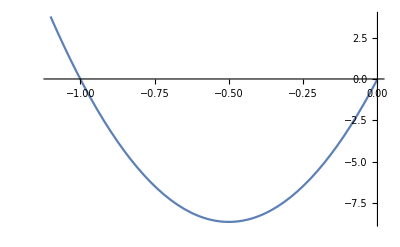

```mathematica
Plot[F1/.u->0,{v,-1.1,0}]
```

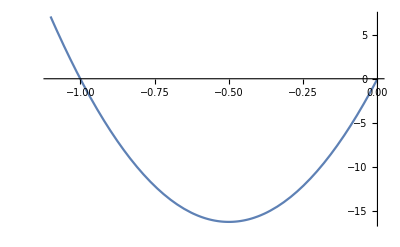

```mathematica
Plot[F2/.u->0,{v,-1.1,0}]
```

#### Assembly

Residual Force at top node:  that node is the second node of th efirst element and the first node of the second element.

```mathematica
Rsys=Fe1⟦2⟧+Fe2⟦1⟧;
Rsys//MatrixForm
```

(-(1050 (4.-u) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))+(1050 (5.5+u) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2))
-(1050 (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))+(1050 (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)))

Remaining stiffnes matrix:

```mathematica
KTsys=Ke1⟦2,2⟧+Ke2⟦1,1⟧;
KTsys//MatrixForm
```

((2100 (4.-u)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(2100 (5.5+u)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (1-(4.-u)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))+(1050 (1-(5.5+u)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)) | (2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2))
(2100 (4.-u) (-0.5-v))/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(2100 (5.5+u) (0.5+v))/(((5.5+u)^2+(0.5+v)^2)^(3/2))-(1050 (4.-u) (-0.5-v) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(((4.-u)^2+(-0.5-v)^2)^(3/2))-(1050 (5.5+u) (0.5+v) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(((5.5+u)^2+(0.5+v)^2)^(3/2)) | (2100 (-0.5-v)^2)/(((4.-u)^2+(-0.5-v)^2)^(3/2))+(2100 (0.5+v)^2)/(((5.5+u)^2+(0.5+v)^2)^(3/2))+(1050 (1-(-0.5-v)^2/((4.-u)^2+(-0.5-v)^2)) Log[0.0615385 ((4.-u)^2+(-0.5-v)^2)])/(√((4.-u)^2+(-0.5-v)^2))+(1050 (1-(0.5+v)^2/((5.5+u)^2+(0.5+v)^2)) Log[0.0327869 ((5.5+u)^2+(0.5+v)^2)])/(√((5.5+u)^2+(0.5+v)^2)))

```mathematica
KTsys/.{u->0,v->0}//MatrixForm
```

(890.065 | -29.8316
-29.8316 | 11.1314)

For the symmetric test case, element (2,2) should be 7.421 and element (1,1) should be 897.9

#### Check the linear problem first

There should be no internal force in the undeformed configuration:

```mathematica
Rsys/.{u->0,v->0}//MatrixForm
```

(0.
0.)

The stiffness matrix should be th elinear stiffness matrix (symetric; not singular!)

```mathematica
KLin=KTsys/.{u->0,v->0};
KLin//MatrixForm
```

(890.065 | -29.8316
-29.8316 | 11.1314)

```mathematica
Det[KLin]
```

9017.7

Try putting a vertical load onto the linear system: 
(the minus signs are due to the sign convention I have chosen.)

```mathematica
Solve[KLin.{u,v}=={0,P},{u,v}]//Simplify
```

{{u→0.+0.00330811 P,v→0.0987019 P}}

### Implement the Newton Algorithm

```mathematica
LoadStep[Pn_,un0_]:=Block[
{Δu,KT,Res,k,TOL,un},
TOL = 10^-12;
k=0;  (* iteration counter *)
un=un0;
Res=Pn-Rsys/.{u->un⟦1⟧,v->un⟦2⟧};
Print["Step ",k," has a residual of ",N[Sqrt[Res.Res],16], " u = ", un ];
While[Sqrt[Res.Res]>TOL && k<20,
KT=KTsys/.{u->un⟦1⟧,v->un⟦2⟧};
(*KT=KTsys/.{u->un0⟦1⟧,v->un0⟦2⟧};*)   (* Modified Newton-Raphson *)
Δu=Inverse[KT].Res;
un=un+Δu;
Res=Pn-Rsys/.{u->un⟦1⟧,v->un⟦2⟧};
k++;
Print["Step ",k," has a residual of ",N[Sqrt[Res.Res],16], ";  u = ", un ];
];
If[k≥20,
Print["--- Warning: solution did not converge after ",k," steps.  Residual force is: ",Sqrt[Res.Res]];
];
un
]
```

```mathematica
Inverse[KLin].{0.,-0.2}
```

{-0.000661622,-0.0197404}

#### Manually trying to find P_cr

P_cr is the load when snap-through will occour.  We can find it approximately by looking for equilibrium with a displacement |v|<0.5 and another one for a slightly larger load that triggers |v|>1, i.e., equilibrium in a far configuration.  Pcr will lie between those two.

```mathematica
Ucr=LoadStep[{0.,-.98},{0.,0.}];
Ucr//MatrixForm
```

Step 0 has a residual of 0.98 u = {0.,0.}

Step 1 has a residual of 0.386652;  u = {-0.00324195,-0.0967279}

Step 2 has a residual of 0.111782;  u = {-0.00439778,-0.150709}

Step 3 has a residual of 0.0307898;  u = {-0.00498225,-0.179611}

Step 4 has a residual of 0.00756295;  u = {-0.00526731,-0.194084}

Step 5 has a residual of 0.00139062;  u = {-0.00538908,-0.200321}

Step 6 has a residual of 0.000106211;  u = {-0.00542271,-0.202047}

Step 7 has a residual of 8.3654×10^-7;  u = {-0.00542569,-0.202201}

Step 8 has a residual of 5.26638×10^-11;  u = {-0.00542572,-0.202202}

Step 9 has a residual of 4.09716×10^-13;  u = {-0.00542572,-0.202202}

(-0.00542572
-0.202202)

This is before snap-through :)

```mathematica
Ucr=LoadStep[{0.,-1.},{0.,0.}];
Ucr//MatrixForm
```

Step 0 has a residual of 1. u = {0.,0.}

Step 1 has a residual of 0.402353;  u = {-0.00330811,-0.0987019}

Step 2 has a residual of 0.125402;  u = {-0.00453243,-0.155956}

Step 3 has a residual of 0.0462655;  u = {-0.00524875,-0.1915}

Step 4 has a residual of 0.042105;  u = {-0.00592318,-0.225916}

Step 5 has a residual of 0.0725081;  u = {-0.00504484,-0.180605}

Step 6 has a residual of 0.0344486;  u = {-0.00564328,-0.211579}

Step 7 has a residual of 35.8138;  u = {-0.0270205,-1.31105}

Step 8 has a residual of 1.32672;  u = {0.00588792,-1.15342}

Step 9 has a residual of 0.196969;  u = {0.00311249,-1.08909}

Step 10 has a residual of 0.00426321;  u = {0.00286588,-1.07944}

Step 11 has a residual of 2.13613×10^-6;  u = {0.0028604,-1.07923}

Step 12 has a residual of 7.19942×10^-13;  u = {0.0028604,-1.07923}

(0.0028604
-1.07923)

This one lies above the snap-through point.  Loads in between failed to converge (properly).

#### Load stepping

Let’s assume Pcr = -0.99 kN and work from there. 
The load levels are

```mathematica
P={0.0,0.25, 0.50, 0.75,0.99, 1.05,1.25, 1.50}*(-0.99)
```

{0.,-0.2475,-0.495,-0.7425,-0.9801,-1.0395,-1.2375,-1.485}

P = {0.0, 0.25, 0.50, 0.75, 0.99, 1.05, .5, 0.}*(-0.99)

```mathematica
U0={0.,0.};
```

```mathematica
U1=LoadStep[{0.,P⟦1⟧},U0];
U1//MatrixForm
```

Step 0 has a residual of 0. u = {0.,0.}

(0.
0.)

```mathematica
U2=LoadStep[{0.,P⟦2⟧},U1];
U2//MatrixForm
```

Step 0 has a residual of 0.2475 u = {0.,0.}

Step 1 has a residual of 0.0252019;  u = {-0.000818757,-0.0244287}

Step 2 has a residual of 0.000170373;  u = {-0.000863771,-0.0264531}

Step 3 has a residual of 8.02913×10^-9;  u = {-0.000864081,-0.026467}

Step 4 has a residual of 2.55169×10^-13;  u = {-0.000864081,-0.026467}

(-0.000864081
-0.026467)

```mathematica
U3=LoadStep[{0.,P⟦3⟧},U2];
U3//MatrixForm
```

Step 0 has a residual of 0.2475 u = {-0.000864081,-0.026467}

Step 1 has a residual of 0.0342423;  u = {-0.00178031,-0.0552992}

Step 2 has a residual of 0.000446522;  u = {-0.00185221,-0.0586226}

Step 3 has a residual of 7.89311×10^-8;  u = {-0.00185317,-0.0586668}

Step 4 has a residual of 7.50936×10^-14;  u = {-0.00185317,-0.0586668}

(-0.00185317
-0.0586668)

```mathematica
U4=LoadStep[{0.,P⟦4⟧},U3];
U4//MatrixForm
```

Step 0 has a residual of 0.2475 u = {-0.00185317,-0.0586668}

Step 1 has a residual of 0.0527655;  u = {-0.00293122,-0.0950199}

Step 2 has a residual of 0.00187419;  u = {-0.00307645,-0.101955}

Step 3 has a residual of 2.60173×10^-6;  u = {-0.00308181,-0.102213}

Step 4 has a residual of 4.68405×10^-12;  u = {-0.00308182,-0.102214}

Step 5 has a residual of 3.66824×10^-13;  u = {-0.00308182,-0.102214}

(-0.00308182
-0.102214)

```mathematica
U5=LoadStep[{0.,P⟦5⟧},U4];
U5//MatrixForm
```

Step 0 has a residual of 0.2376 u = {-0.00308182,-0.102214}

Step 1 has a residual of 0.102185;  u = {-0.00446605,-0.15392}

Step 2 has a residual of 0.0275982;  u = {-0.00501618,-0.181315}

Step 3 has a residual of 0.00672482;  u = {-0.00528482,-0.194971}

Step 4 has a residual of 0.00121145;  u = {-0.00539847,-0.200793}

Step 5 has a residual of 0.0000873256;  u = {-0.00542897,-0.20236}

Step 6 has a residual of 6.01864×10^-7;  u = {-0.0054315,-0.20249}

Step 7 has a residual of 2.93386×10^-11;  u = {-0.00543151,-0.202491}

Step 8 has a residual of 3.67208×10^-13;  u = {-0.00543151,-0.202491}

(-0.00543151
-0.202491)

```mathematica
P⟦5⟧
```

-0.9801

```mathematica
U6=LoadStep[{0.,P⟦6⟧},U5];
U6//MatrixForm
```

Step 0 has a residual of 0.0594 u = {-0.00543151,-0.202491}

Step 1 has a residual of 1.02764;  u = {-0.00892656,-0.376522}

Step 2 has a residual of 0.379027;  u = {-0.00700238,-0.267952}

Step 3 has a residual of 0.132272;  u = {-0.00562897,-0.205846}

Step 4 has a residual of 2.18875;  u = {-0.0106012,-0.462875}

Step 5 has a residual of 0.938584;  u = {-0.00794294,-0.289199}

Step 6 has a residual of 0.15028;  u = {-0.00597157,-0.222493}

Step 7 has a residual of 1.0348;  u = {-0.00267058,-0.0544058}

Step 8 has a residual of 0.258682;  u = {-0.00414427,-0.135344}

Step 9 has a residual of 0.114289;  u = {-0.00529598,-0.190876}

Step 10 has a residual of 0.250496;  u = {-0.00695632,-0.275388}

Step 11 has a residual of 0.132574;  u = {-0.00577079,-0.213039}

Step 12 has a residual of 213.248;  u = {0.0331116,1.7875}

Step 13 has a residual of 50.8654;  u = {0.0709072,0.943131}

Step 14 has a residual of 15.6129;  u = {0.015733,0.467365}

Step 15 has a residual of 4.53231;  u = {0.00504991,0.183427}

Step 16 has a residual of 1.43229;  u = {-0.000625657,0.00923988}

Step 17 has a residual of 0.463664;  u = {-0.0032869,-0.0964597}

Step 18 has a residual of 0.167634;  u = {-0.00472338,-0.16268}

Step 19 has a residual of 0.1071;  u = {-0.00581559,-0.217065}

Step 20 has a residual of 4.44014;  u = {0.000762882,0.122167}

--- Warning: solution did not converge after 20 steps.  Residual force is: 4.44014

(0.000762882
0.122167)

This load step did not converge and the obtained displacement is  not an equilibrium state.  Let’s try once again with a different initial state.  That starting state, unlike before, will not be an equilibrium state.  We know that there will be snap-through, so let’s move the previous eqilibrium solution by 2 x height.

```mathematica
U6=LoadStep[{0.,P⟦6⟧},U5+{0.0,-1.0}];
U6//MatrixForm
```

Step 0 has a residual of 12.2063 u = {-0.00543151,-1.20249}

Step 1 has a residual of 0.443895;  u = {0.00381773,-1.10736}

Step 2 has a residual of 0.0271102;  u = {0.00299448,-1.08316}

Step 3 has a residual of 0.0000832442;  u = {0.00296048,-1.08181}

Step 4 has a residual of 7.95733×10^-10;  u = {0.00296037,-1.08181}

Step 5 has a residual of 2.3537×10^-14;  u = {0.00296037,-1.08181}

(0.00296037
-1.08181)

This got us close enough to an equilibrium state and, thus, converged.

```mathematica
U7=LoadStep[{0.,P⟦7⟧},U6];
U7//MatrixForm
```

Step 0 has a residual of 0.198 u = {0.00296037,-1.08181}

Step 1 has a residual of 0.00757152;  u = {0.00345971,-1.09466}

Step 2 has a residual of 5.69855×10^-6;  u = {0.00345111,-1.09431}

Step 3 has a residual of 3.46036×10^-12;  u = {0.0034511,-1.09431}

Step 4 has a residual of 1.99484×10^-13;  u = {0.0034511,-1.09431}

(0.0034511
-1.09431)

```mathematica
U8=LoadStep[{0.,P⟦8⟧},U7];
U8//MatrixForm
```

Step 0 has a residual of 0.2475 u = {0.0034511,-1.09431}

Step 1 has a residual of 0.0107184;  u = {0.00405421,-1.10952}

Step 2 has a residual of 0.0000103841;  u = {0.00404252,-1.10904}

Step 3 has a residual of 1.0412×10^-11;  u = {0.0040425,-1.10904}

Step 4 has a residual of 1.84891×10^-13;  u = {0.0040425,-1.10904}

(0.0040425
-1.10904)

#### Plotting the results

```mathematica
LoadPath=Transpose[{U1,U2,U3,U4,U5,U6,U7,U8}]
```

{{0.,-0.000864081,-0.00185317,-0.00308182,-0.00543151,0.00296037,0.0034511,0.0040425},{0.,-0.026467,-0.0586668,-0.102214,-0.202491,-1.08181,-1.09431,-1.10904}}

```mathematica
{LoadPath⟦1⟧,P}
```

{{0.,-0.000864081,-0.00185317,-0.00308182,-0.00543151,0.00296037,0.0034511,0.0040425},{0.,-0.2475,-0.495,-0.7425,-0.9801,-1.0395,-1.2375,-1.485}}

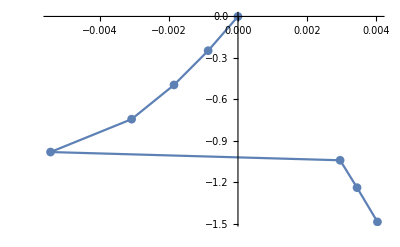

```mathematica
ListPlot[Transpose[{LoadPath⟦1⟧,P}],Joined->True,PlotMarkers->Automatic]
```

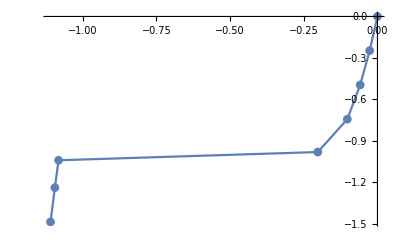

```mathematica
ListPlot[Transpose[{LoadPath⟦2⟧,P}],Joined->True,PlotMarkers->Automatic]
```

#### Some more debugging - not significant

```mathematica
Rsys/.u->0//Simplify;
%//MatrixForm
```

(-(4200. Log[1.+0.0615385 v+0.0615385 v^2])/(√(16.25+1. v+v^2))+(5775. Log[0.0327869 (30.25+(0.5+v)^2)])/(√(30.25+(0.5+v)^2))
1050 (0.5+v) (Log[1.+0.0615385 v+0.0615385 v^2]/(√(16.25+1. v+v^2))+Log[0.0327869 (30.25+(0.5+v)^2)]/(√(30.25+(0.5+v)^2))))

```mathematica
Rsys/.u->0
```

{-(4200. Log[0.0615385 (16.+(-0.5-v)^2)])/(√(16.+(-0.5-v)^2))+(5775. Log[0.0327869 (30.25+(0.5+v)^2)])/(√(30.25+(0.5+v)^2)),-(1050 (-0.5-v) Log[0.0615385 (16.+(-0.5-v)^2)])/(√(16.+(-0.5-v)^2))+(1050 (0.5+v) Log[0.0327869 (30.25+(0.5+v)^2)])/(√(30.25+(0.5+v)^2))}

Horizontal force:

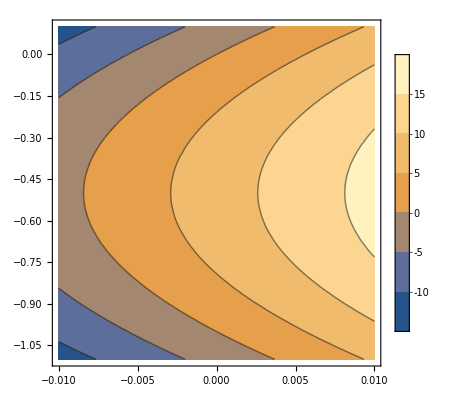

```mathematica
ContourPlot[Evaluate[Rsys⟦1⟧],{u,-0.01,0.01},{v,-1.1,0.1},PlotRange->All,PlotLegends->Automatic]
```

Vertical force:

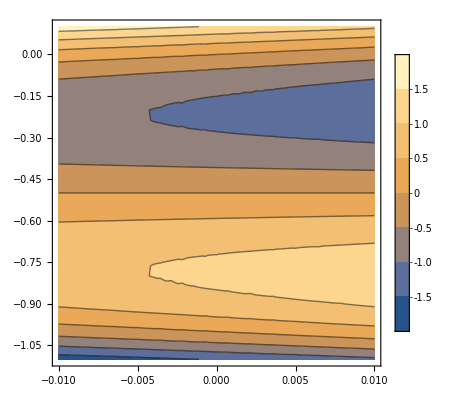

```mathematica
ContourPlot[Evaluate[Rsys⟦2⟧],{u,-0.01,0.01},{v,-1.1,0.1},PlotRange->All,PlotLegends->Automatic]
```

```mathematica
Rsys/.{u->0.0,v->-0.12}
```

{3.18191,-0.898433}

```mathematica
KTsys/.{u->0.0,v->-0.12}//MatrixForm
```

(897.054 | -23.1299
-23.1299 | 4.13843)

```mathematica
ϵ[λ2[x1,x2,u1,{0.0,-0.12}]]
```

-0.00173415

```mathematica
EA
```

2100